Variational Theorem

Suppose we have a Hamiltonian H whose eigenstates u_n and energies E_n , n=0,1,… are unknown to us.  Let us make a guess ψ_g for the ground state wavefunction.  The expectation value of H with ψ_g is

ψ_gHψ_g=∑_n ψ_gnnHψ_g=∑_n E_n ψ_gnnψ_g

Since E_n≥ E_0,

ψ_gHψ_g=∑_n E_n ψ_gnnψ_g≥E_0∑_n ψ_gnnψ_g=E_0 
→ψ_gHψ_g≥E_0

This is the variational principle.  It says that whatever guess we make, no matter how bad, the expectation value will always be greater than the actual ground state energy.  So if we make our guess have a set of adjustable parameters, we can minimize ψ_gHψ_g  with respect to those parameters and get an upper limit on the ground-state energy.

As an example, let’s guess a Gaussian for the wavefunction of the 1s state of Hydrogen:

```mathematica
$Assumptions=α>0
```

α>0

```mathematica
psi=r Exp[-α r^2];psi=psi/(Integrate[psi^2,{r,0,∞}]^(1/2))
```

(2 2^(3/4) ⅇ^(-r^2 α) r)/(π^(1/4) √(1/α^(3/2)))

```mathematica
With[{ψ=psi},Integrate[ψ(-1/2 D[ψ, r,r]-1/r ψ),{r,0,∞}]]
```

-2 √(2/π) √α+(3 α)/2

Minimize w.r.t. α:

```mathematica
Minimize[%,α]
```

{-4/(3 π),{α→8/(9 π)}}

So our upper limit on the ground state energy is

```mathematica
-4/(3 π)≥ -1/2
```

True

```mathematica
-4/(3 π)//N
```

-0.424413

second example:  s^3 potential

```mathematica
$Assumptions=z>0
```

z>0

normalize the guess

```mathematica
With[{psi=s ⅇ^(-z s^2)},Integrate[psi psi,{s,0,∞}]]
```

(√(π/2))/(8 z^(3/2))

variational theory with V=s^3.  Find expectation value of H:

```mathematica
With[{psi=(s ⅇ^(-z s^2))/Sqrt[(√(π/2))/(8 z^(3/2))]},Integrate[psi (-1/2 D[psi,{s,2}]+s^3 psi),{s,0,∞}]]
```

(√(2/π))/z^(3/2)+(3 z)/2

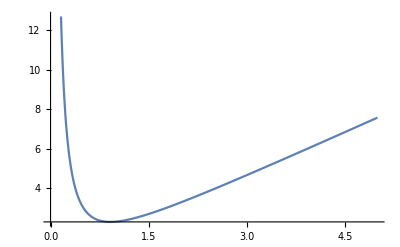

```mathematica
Plot[%,{z,0,5}]
```

find the minimum as a function of z

```mathematica
Minimize[(√(2/π))/z^(3/2)+(3 z)/2,z]
```

{5/(2^(4/5) π^(1/5)),{z→(2/π)^(1/5)}}

```mathematica
%//N
```

{2.2841,{z→0.913642}}

So this is an upper limit on the energy.  Now solve with NDSolve to see how good this number is

```mathematica
p2[s_]=With[{e=2.2765},NDSolve[{-1/2 D[p[s],{s,2}]+s^3 p[s]==e p[s],p[15]==1,p'[15]== -1},p[s],{s,15,0}]//Tr]⟦2⟧;
p2[0]/p2'[0]
```

9.02533×10^-6

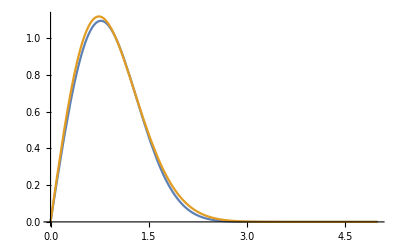

```mathematica
Plot[{p2[s]/p2[1],s (ⅇ^(-z s^2))/ⅇ^-z/.z->.9136},{s,0,5}]
```

## Excited states

The question arose in class about how to extend the variational principle to excited states.  Suppose we make our guess for the excited state as ψ_1, chosen to be orthogonal to the exact ground state u_0.

ψ_1Hψ_1=∑_n E_n ψ_1nnψ_1

Since nψ_1=0, there is no n=0  contribution to this sum, which becomes

ψ_1Hψ_1=∑_(n=1) E_n ψ_1nnψ_1≥E_1∑_(n=0) ψ_1nnψ_1=E_1 ψ_1ψ_1

The weakness in this is that it assumes we know the exact ground state.  But it does suggest that if we think our variational ground state is pretty good, we might get an upper bound on the excited state energy as well.

Returning to the hydrogen atom, let’s guess

```mathematica
psi0=(HermiteH[1,α r]Exp[(-(α r)^2)/2])/(Integrate[(HermiteH[1,α s]Exp[(-(α s)^2)/2])^2,{s,0,∞}]^(1/2))
```

(2 ⅇ^(-1/2 r^2 α^2) r)/(π^(1/4) (1/α)^(3/2))

```mathematica
psi1=(HermiteH[3,α r]Exp[(-(α r)^2)/2])/(Integrate[(HermiteH[3,α s]Exp[(-(α s)^2)/2])^2,{s,0,∞}]^(1/2))
```

(ⅇ^(-1/2 r^2 α^2) (-12 r α+8 r^3 α^3))/(2 √6 π^(1/4) √(1/α))

```mathematica
Integrate[psi0 psi1,{r,0,∞}]
```

0

We already found the optimum value of α; orthogonality would require α to be the same for the excited state.  So our guess for the 1st excited state energy would be

```mathematica
With[{ψ=psi1/.α->8/(9 π)},Integrate[ψ(-1/2 D[ψ, r,r]-1/r ψ),{r,0,∞}]]
```

-(8 (-14+15 √π))/(81 π^2)

```mathematica
%//N
```

-0.125957

you can see that the result, though impressively close to the correct answer of -1/8, is actually less than the experimental excited-state energy.  Because we, in principle, do not know the exact ground state, we cannot be sure of the sign of the error; no bounds can be placed.